# Entanglement as Route to Decoherence

The expectation values for the components of the spin measuring device exhibit motion, called precession, demonstrated in the animation given below.

```mathematica
ClearAll["Global`*"]
sx[θ_,t_]:=Cos[θ]Re[Exp[I ω t ]]
sy[θ_,t_]:=-Sin[θ]Im[Exp[I ω t ]]
sz[θ_,t_]:=Cos[θ]
vector[θ_,t_]:=Arrow[Tube[{{0,0,0},{sx[θ,t],sy[θ,t],sz[θ,t]}},0.025]]
bloch[θ_,t_]:=Show[Graphics3D[{Specularity[White,100],Lighting->{{"Point",Cyan,{1,0,1}}},Opacity[0.2],Sphere[{0,0,0}]}],Graphics3D[{Red,vector[θ,t]}],Boxed->False,ViewPoint->{Infinity,0,0},PlotRange->{{-1,1},{-1,1},{-1,1}}]
```

```mathematica
ω=1;
Animate[bloch[Pi/4,t],{t,0,2Pi},SaveDefinitions->True]
```

This behavior is important in applications such as magnetic resonance imaging (MRI). In the latter, a spin-1/2 particle (usually the nucleus of an atom) is subjected to a strong magnetic field along the z-direction. The
field induces the Hamiltonian H_0 given above. Another external field pulse puts the state of the particle in a superposition of the spin-up (|0⟩)  and spin-down (|1⟩ ) states, as in |ψ_0⟩ given above. The superposition
generates the precessional motion. During this motion, the charged particle emits radiation characterised by the frequency ω of the precession. The value of the latter is sensitive to the atom’s location and  neighboring molecules. By studying the dependence of ω in different locations of a tissue sample, on can conjure
a physical “picture” of the sample. 

This scenario is applicable as long as the precession survives, i.e. the density matrix describing the system is that of a pure state. For various reasons, coherence is temporary and eventually the density  matrix evolves into that describing a mixed state. Precessional motion decays as the system relaxes into a state characterized by a mixed state density matrix. This process is called decoherence. Here, we will explore one mechanism by with a pure state evolves into a mixed state, or how  decoherence  emerges.

## Environmental Qubits

Before we explore the route to decoherence, lets generalize our single-qubit system by adding one additional qubit, resulting in a 4-dimensional Hilbert space. We call the additional qubit an environmental qubit, as we will not be interested in its properties in a measurement of the system qubit. In the text, we showed how neglect of the environmental qubit is equivalent to taking the partial trace, within the sub-space of the environment Hilbert space, from the total 4-d density matrix.

Thus, with choice of Hamiltonian (2) in which the system qubit and environmental qubit are decoupled, the system density matrix is unaffected by tracing over the environmental Hilbert space. The system evolves
in the same way described above for a single qubit system and it does not experience decoherence. We now
consider this same 2-qubit Hilbert but allow allow Hamiltonian evolution with a new Hamiltonian described below.

So with this example we have demonstrated how a decoherence is precipitated when the system qubit is entangled, due to the properties of H_int, with an environmental qubit.

## Time Evolution of a Qubit Pure State to a Mixed State

### Signatures of Decoherence

For our numerical demonstration we choose the value ω=1, assume n=7, and choose a uniform distribution of values for the coefficients c_i.

```mathematica
nq=7;
dim=2^7;
ω=1;
c=Table[RandomReal[{0,10}],{i,1,dim}];
cnorm=c/Sqrt[Total[c^2]];
cnorm.cnorm
```

1.

Further for the energy eigenvalues ℏ ω_i we choose a Gaussian distribution of frequencies centered
around the value ω/2, so that the phases e^(i ω_i t) are given by the expression

```mathematica
phases=Table[Exp[I t RandomVariate[NormalDistribution[ω,0.1]]],{i,1,dim}];
```

and ψ_1(t), ψ_0  are given by

```mathematica
ψ1=Exp[I ω t]phases cnorm;
ψ0=cnorm;
```

Thus, the overlap r(t) is

```mathematica
r[t_]=ψ0.ψ1;
```

Using expression (1), we construct and plot S_X(t), S_Y(t) (taking the value of ℏ=2), and the polar angle θ=45 degrees.

```mathematica
sx[θ_,t_]:=Sin[θ]Re[Exp[I ω t] r[t]]
sy[θ_,t_]:=-Sin[θ]Im[Exp[I ω t] r[t]]
sz[θ_,t_]:=Cos[θ]
```

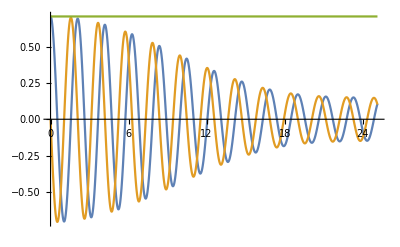

```mathematica
Plot[{sx[Pi/4,t],sy[Pi/4,t],sz[Pi/4,t]},{t,0,8Pi/ω}]
```

The amplitudes for the expectation values of S_X(t), S_Y(t) decays for large t. Likewise, if we plot the time development of the vector ⟨S⃗⟩,

```mathematica
Animate[bloch[Pi/4,t],{t,0,8Pi/ω},SaveDefinitions->True]
```

From this animation we notice that (a) for t  near t=0, the vector ⟨S⃗⟩ precesses  on the surface of the Bloch sphere in the same manner as in the single qubit example described above. (b) for larger values of t, the vector’s length is less than the radius of the Bloch sphere and is due to the fact that Tr[ρ(t).ρ(t)] < 1. (c) For sufficiently large values of t, the system relaxes to an almost stationary vector pointing along the z - axis of the Bloch sphere.

#### Exercises

(1) Show that if the partial trace is not carried out, the total (system+environment) density matrix describes a pure state at all values for t.

(2) Convince yourself that no energy is transferred between the system qubit and the environmental qubits.  Can you conclude that de-coherence, in this model, is solely due to entanglement of the system qubit  with the environment ?